```mathematica
$Assumptions={a0>0,b0>0};
ansCF=MatrixPower[{{1,-α},{-β,1}},n].{a0,b0}//FullSimplify
CFta=Solve[First[ansCF]==0,n]//FullSimplify
CFtb=Solve[Last[ansCF]==0,n]//FullSimplify
```

{((b0 √α+a0 √β) (1-√α √β)^n+(-b0 √α+a0 √β) (1+√α √β)^n)/(2 √β),((b0 √α+a0 √β) (1-√α √β)^n+(b0 √α-a0 √β) (1+√α √β)^n)/(2 √α)}

{{n→(ⅈ π+2 ArcTanh[(b0 √α)/(a0 √β)])/(2 ArcTanh[√α √β])}}

{{n→(ⅈ π+2 ArcTanh[(a0 √β)/(b0 √α)])/(2 ArcTanh[√α √β])}}

```mathematica
$Assumptions={a0>0,k1>0};
ansCF=MatrixPower[{{1,-α},{-k1 α,1}},n].{a0,k2 a0};
FullSimplify[Solve[Last[ansCF]==0,n]]
```

{{n→(ⅈ π-Log[-√k1+k2]+Log[√k1+k2])/(2 ArcTanh[√k1 α])}}

```mathematica
$Assumptions={a0>0,b0>0,α>0,β>0};
ansWF=DSolveValue[{a'[t]==-β b[t],b'[t]==-α a[t],a[0]==a0,b[0]==b0 },{a[t],b[t]},t]//FullSimplify;
Solve[Last[ansWF]==0,t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[-(√(-a0 α-b0 √(α β)))/(√(-a0 α+b0 √(α β)))])/(√(α β)),C[1]∈Integers]},{t→ConditionalExpression[(2 ⅈ π C[1]+Log[(√(-a0 α-b0 √(α β)))/(√(-a0 α+b0 √(α β)))])/(√(α β)),C[1]∈Integers]}}

```mathematica
$Assumptions={a0>0,b0>0,α>0,β>0};
ansWF=DSolveValue[{a'[b[t]]==(β b[t])/(α a[t]),a[0]==a0,b[0]==b0 },{a,b},t]//FullSimplify;
```

DSolve::nestdv: 表达式 b[t] 具有嵌套的应变量.

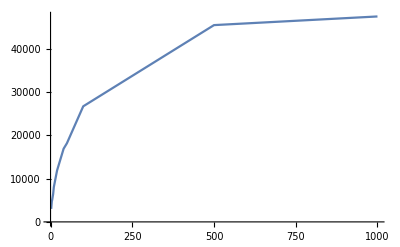

```mathematica
data={{2,3010},{4,4800},{5,5080},{8,6455},{10,8030},{20,11900},{40,16920},{50,18170},{100,26725},{500,45500},{1000,47500}};
ListLinePlot[data]
```

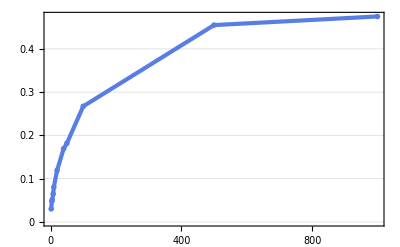

{a→140.876,b→0.779026}

```mathematica
data={{2,301/10000},{4,6/125},{5,127/2500},{8,1291/20000},{10,803/10000},{20,119/1000},{40,423/2500},{50,1817/10000},{100,1069/4000},{500,91/200},{1000,19/40}};
Show[ListLinePlot[data,PlotTheme->"Business"]]
model=0.5- E^(-x/a-b);
fit=FindFit[data,model,{a,b},x]
```

```mathematica
FindFormula[data,x,5]
```

{0.176445,0.719276,Cos[x],Sin[x],0.195115+Sin[Csc[x]]}

```mathematica
ansWF=DSolve[{
a'[t]==-0.01c[t],
b'[t]==-0.01c[t],
c'[t]==-0.015a[t]-0.025b[t],
a[0]==A,b[0]==100-A ,c[0]==100}
,{a[t],b[t],c[t]},t]
```

{{a[t]→0.625 ⅇ^(-0.02 t) (90.+0.3 A-100. ⅇ^(0.02 t)+1. A ⅇ^(0.02 t)+10. ⅇ^(0.04 t)+0.3 A ⅇ^(0.04 t)),b[t]→-0.375 ⅇ^(-0.02 t) (-150.-0.5 A-100. ⅇ^(0.02 t)+1. A ⅇ^(0.02 t)-16.6667 ⅇ^(0.04 t)-0.5 A ⅇ^(0.04 t)),c[t]→-0.375 ⅇ^(-0.02 t) (-300.-1. A+33.3333 ⅇ^(0.04 t)+1. A ⅇ^(0.04 t))}}

```mathematica
ansWF/.Rule->Equal
```

{{a[t]==0.625 ⅇ^(-0.02 t) (90.+0.3 A-100. ⅇ^(0.02 t)+1. A ⅇ^(0.02 t)+10. ⅇ^(0.04 t)+0.3 A ⅇ^(0.04 t)),b[t]==-0.375 ⅇ^(-0.02 t) (-150.-0.5 A-100. ⅇ^(0.02 t)+1. A ⅇ^(0.02 t)-16.6667 ⅇ^(0.04 t)-0.5 A ⅇ^(0.04 t)),c[t]==-0.375 ⅇ^(-0.02 t) (-300.-1. A+33.3333 ⅇ^(0.04 t)+1. A ⅇ^(0.04 t))}}

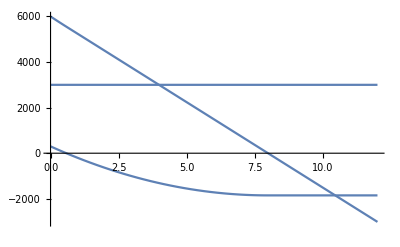

```mathematica
Zero[x_]:=HeavisideTheta[x]x
sol=ParametricNDSolveValue[{
a'[t]==-0.16  Zero[b[t]]-0.25  Zero[c[t]],
b'[t]==-0.09  k Zero[a[t]],
c'[t]==-0.04 (1-k)Zero[a[t]],
WhenEvent[b[t]=0,c'[t]->-0.04 Zero[a[t]]],
WhenEvent[c[t]=0,b'[t]->-0.09  Zero[a[t]]],
a[0]==6000,b[0]==6000-5700k ,c[0]==1800+1200 k}
,{a[t],b[t],c[t]},{t,0,20},k];
Plot[sol[1],{t,0,12}]
```

```mathematica
Zero[x_]:=HeavisideTheta[x]x
sol=ParametricNDSolveValue[{
a'[t]==-0.16  Zero[b[t]]-0.25  Zero[c[t]],
b'[t]==-0.09  k Zero[a[t]],
c'[t]==-0.04 (1-k)Zero[a[t]],
WhenEvent[b[t]==0,val=Sqrt[a[t]^2-0.04c[t]^2/0.25]],
a[0]==6000,b[0]==6000-5700k ,c[0]==4800+1200 k}
,{a[t],b[t],c[t]},{t,0,20},k];
f[k_]:=Module[{},sol[k];val]
Table[{i,f[i]},{i,1,0.85,-(1-0.85)/20}]
```

{{1.,4481.07},{0.9925,4307.68},{0.985,4307.68},{0.9775,3928.61},{0.97,3719.54},{0.9625,3494.27},{0.955,3249.38},{0.9475,2979.94},{0.94,2678.47},{0.9325,2332.46},{0.925,2332.46},{0.9175,1373.6},{0.91,256.724},{0.9025,0.+1336.07 ⅈ},{0.895,0.+1914.89 ⅈ},{0.8875,0.+1914.89 ⅈ},{0.88,0.+1914.89 ⅈ},{0.8725,0.+1914.89 ⅈ},{0.865,0.+1914.89 ⅈ},{0.8575,0.+1914.89 ⅈ},{0.85,0.+1914.89 ⅈ}}

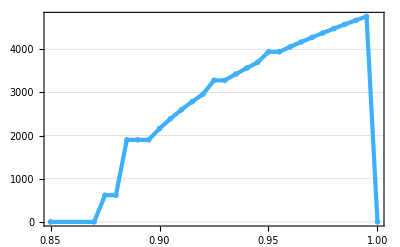

```mathematica
ListLinePlot[{{1.,4760.12415933601},{0.999925,4760.12415933601},{0.99985,4760.12415933601},{0.999775,4760.12415933601},{0.9997,4760.12415933601},{0.999625,4760.12415933601},{0.99955,4760.12415933601},{0.999475,4760.12415933601},{0.9994000000000001,4760.12415933601},{0.999325,4760.12415933601},{0.99925,4760.12415933601},{0.999175,4760.12415933601},{0.9991,4760.12415933601},{0.999025,4760.12415933601},},PlotTheme->"Business",PlotStyle->96]
```

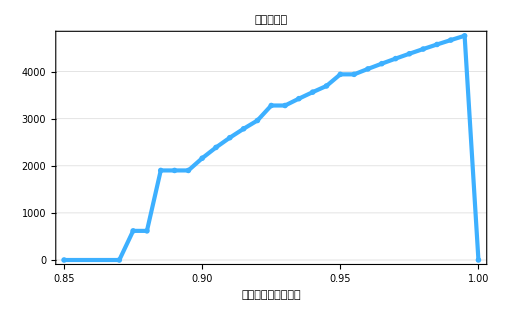

```mathematica
Show[%964,FrameLabel->{{None,None},{HoldForm[轻步兵重点攻击比例],None}},PlotLabel->HoldForm[留存数量图],LabelStyle->{FontFamily->"萝莉体 第二版",16,GrayLevel[0]}]
```